## EccentricPN

A Mathematica package for generating eccentric PN waveforms.  Under construction.

### Load the package

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/ian/Projects/eccentricpn

```mathematica
Get["EccentricPN.m"]
```

Computing kappaE

2.69221

Computing kappaJ

2.59374

### Choose the evolution parameters

Length of the evolution

```mathematica
tMax=1800;
```

Time discretization for certain operations

```mathematica
dt=10;
```

Initial conditions

```mathematica
n0=0.016; e0=0.1;l0=0;phi0=0;
```

```mathematica
x0=Normal[xInne]/.{n->n0,e->e0,eta->0.25}
```

0.0756337

### Do an evolution with the (n,e) model

```mathematica
neSoln=EccentricSoln[neModel,{n0,e0,l0,phi0},0,{0,tMax,dt}]
```

{r→InterpolatingFunction[{{0.,1800.}},<>],om→InterpolatingFunction[{{0.,1800.}},<>],phi→InterpolatingFunction[{{0.,1800.}},<>],n→InterpolatingFunction[{{-30.,1830.}},<>],e→InterpolatingFunction[{{-30.,1830.}},<>],u→InterpolatingFunction[{{0.,1800.}},<>],h→InterpolatingFunction[{{0.,1800.}},<>],psi4→InterpolatingFunction[{{0.,1800.}},<>],psi4Om→InterpolatingFunction[{{0.,1800.}},<>],psi4Phi→InterpolatingFunction[{{0.,1800.}},<>]}

### Do an evolution with the (x,e) model

```mathematica
soln=EccentricSoln[xeModel,{x0,e0,l0,phi0},0,{0,tMax,dt}]
```

{r→InterpolatingFunction[{{0.,1800.}},<>],om→InterpolatingFunction[{{0.,1800.}},<>],phi→InterpolatingFunction[{{0.,1800.}},<>],x→InterpolatingFunction[{{-30.,1830.}},<>],e→InterpolatingFunction[{{-30.,1830.}},<>],u→InterpolatingFunction[{{0.,1800.}},<>],h→InterpolatingFunction[{{0.,1800.}},<>],psi4→InterpolatingFunction[{{0.,1800.}},<>],psi4Om→InterpolatingFunction[{{0.,1800.}},<>],psi4Phi→InterpolatingFunction[{{0.,1800.}},<>]}

### Coordinate motion

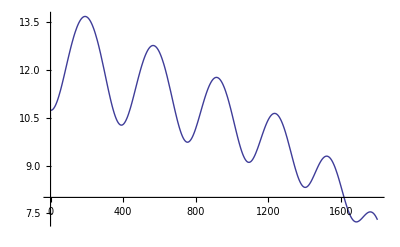

```mathematica
Plot[Evaluate[{r[t]/.soln}],{t,0,tMax}]
```

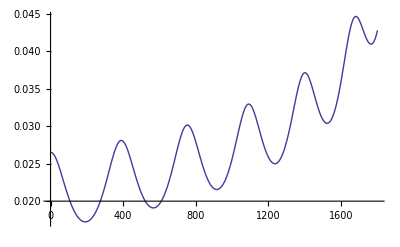

```mathematica
Plot[Evaluate[{om[t]/.soln}],{t,0,tMax}]
```

### Eccentricity

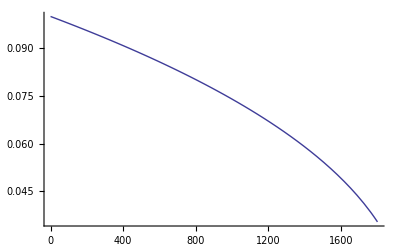

```mathematica
Plot[Evaluate[{e[t]/.soln}],{t,0,tMax},PlotRange->{0,All}]
```

### Waveforms

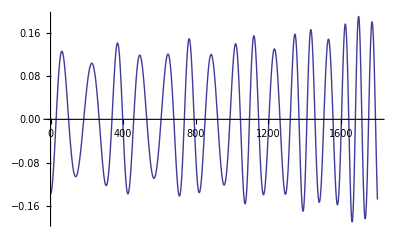

```mathematica
Plot[Evaluate[{Re[h[t]]/.soln}],{t,0,tMax}]
```

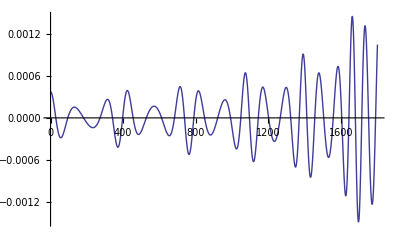

```mathematica
Plot[Evaluate[{Re[psi4[t]]/.soln}],{t,0,tMax}]
```

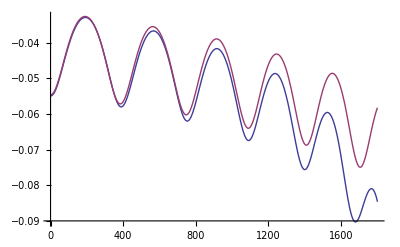

```mathematica
Plot[Evaluate[{psi4Om[t]/.soln,psi4Om[t]/.neSoln}],{t,0,tMax}]
```